```mathematica
(* Simple Models *)
```

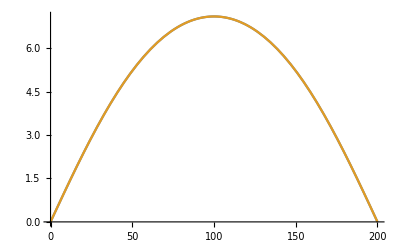

(0 | 0 | 10 Cos[99.5 t] tanhWindow[t,20,200] | 10 Cos[99.5 t] tanhWindow[t,20,200]
0 | 5 | 10 Cos[(94.5-2 (1-t/100)) t] tanhWindow[t,20,200] | -10 Cos[(94.5-2 (1-t/100)) t] tanhWindow[t,20,200]
10 Cos[99.5 t] tanhWindow[t,20,200] | 10 Cos[(94.5-2 (1-t/100)) t] tanhWindow[t,20,200] | 100 | 0
10 Cos[99.5 t] tanhWindow[t,20,200] | -10 Cos[(94.5-2 (1-t/100)) t] tanhWindow[t,20,200] | 0 | 101)

$Aborted

$Aborted

```mathematica
Clear[H, f1, f2, A, B, ω1, ω2, t, δ1, δϵ, ϵ];

Tmax = 200;
A[t_] := 10*tanhWindow[t, Tmax/10, Tmax]
B[t_] := 10*tanhWindow[t, Tmax/10, Tmax]

Plot[{A[t], B[t]}, {t, 0, Tmax}]

f1[t_] := A[t]*Cos[ω1*t]
f2[t_] := B[t]*Cos[ω2*t]

δ1 = 5;
δϵ = 1;
ϵ = 100;
ω1 = 99.5;
ω2 = ω1 - δ1 - 2*(1 - 2*t/Tmax);

H = {
{0, 0, f1[t], f1[t]},
{0, δ1, f2[t], -f2[t]},
{f1[t], f2[t], ϵ, 0},
{f1[t], -f2[t], 0, ϵ + δϵ}
};
Htrans = {
{0, 0, A[t]/2, A[t]/2},
{0, δ1 + ω2 - ω1, B[t]/2, -B[t]/2},
{A[t]/2, B[t]/2, ϵ - ω1, 0},
{A[t]/2, -B[t]/2, 0, ϵ + δϵ - ω1}
};

H // MatrixForm


ψ0 = {0, 1, 0, 0};
funcs=Array[ψ[#1][t]&,{Length[ψ0]}];
equations=Flatten@Join[Thread[H.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
state= NDSolveValue[equations,funcs,{t,-Tmax/100,101*Tmax/100}, MaxSteps->10^7, AccuracyGoal->10];
LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->{1, 2, 3, 4}]
```

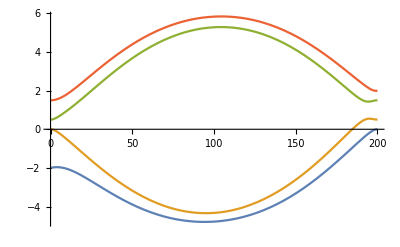

```mathematica
Es = Eigenvalues[Htrans];
Plot[Es, {t, 0, Tmax}]
```

```mathematica
(* Full Hamiltonian *)
```

(0 | -701921. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | 1.09564×10^8-1.15085×10^9 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | 0
-701921. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | -2.05557×10^8 | 7.74737×10^7-8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 1.13945×10^9 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | 1.82435×10^8+8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 1.83783×10^8 | 0
8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 7.74737×10^7-8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 3.53101×10^10 | -496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | -496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | 5.24806×10^7-8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2
0 | 1.13945×10^9 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | -496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 3.52884×10^10 | 0 | -496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | 7.42188×10^7-1.15085×10^9 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2
1.09564×10^8-1.15085×10^9 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | -496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | 3.53319×10^10 | 496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 1.13945×10^9 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0
8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 1.82435×10^8+8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | -496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 496333. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 3.49426×10^10 | -2.07428×10^8-8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | -8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2
0 | 1.83783×10^8 | 5.24806×10^7-8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | 1.13945×10^9 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | -2.07428×10^8-8.1377×10^8 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 7.04583×10^10 | -701921. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2
0 | 0 | 8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 7.42188×10^7-1.15085×10^9 Cos[3.49644×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 0 | -8.05713×10^8 Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | -701921. Cos[3.47588×10^10 t] tanhWindow[t,1/20000000,1/2000000]^2 | 7.06203×10^10)

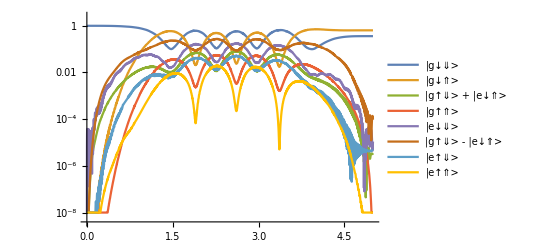

{0.360462,0.639438,2.95808×10^-6,1.74954×10^-9,0.0000108689,0.0000957315,4.4159×10^-6,2.97584×10^-14}

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
clearStatus[]:=showStatus[""];
clearStatus[]

clearVariables[]
setVariables[]

ΔE = 0;
Bac = 0;
Eac = 0;

Clear[B0];
B0sol = NSolve[H[[3]][[3]] == H[[6]][[6]], B0][[1]];
B0 = (B0 /. B0sol);
Vt = Vt;
d = d*1.01;

Clear[Bac]
Clear[Eac]

Htrans = transform[H, Λ];
Mtrans = 2*π*Htrans // N // FullSimplify;
Mtrans = transform[Mtrans, IdentityMatrix[8]*E^(ⅈ*Mtrans[[1]][[1]]*t)] // FullSimplify // Chop;

Tmax = 1.6*10^-7;

δ1 = Mtrans[[2]][[2]];

ϵ = Mtrans[[6]][[6]];
δϵ = Mtrans[[3]][[3]] - ϵ;

Eamp[t_] := 60*tanhWindow[t, Tmax/10, Tmax]^2
Bamp[t_] := Eamp[t]*(8.057132424585235*^6)/(6.213371789014474*^10)

Clear[ω1, ω2, Eac, Bac]
ω1[t_] := ϵ - .5*δϵ
ω2[t_] := ω1[t] - δ1 + .1*δϵ*(1 - 2*t/Tmax)

Bac = Bamp[t]*Cos[ω1[t]*t];
Eac = Eamp[t]*Cos[ω2[t]*t];

Mtrans // FullSimplify // MatrixForm

(* simulate Mtrans *)
Clear[ψ];
ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};
funcs=Array[ψ[#1][t]&,{Length[ψ0]}];
equations=Flatten@Join[Thread[Mtrans.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
state= NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]];
LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGERotated]
Abs[state]^2 /. t->Tmax
```